```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\Ag_EG_vac\111Ag\pmf_curve\100_windows_umbrella_sampling\10ns\k_0.7\ui\auto3

```mathematica
log=OpenRead["plotdA.txt"];
dA=ReadList[log,Number];Close[log];
```

```mathematica
log=OpenRead["plotStd.txt"];
Std=ReadList[log,Number];Close[log];
```

```mathematica
log=OpenRead["plotSS.txt"];
Step=ReadList[log,Number];Close[log];
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
TotalRunNs=Input["Total time run (ns)",7]
```

10

```mathematica
SetSkip=Input["Skip time (ns)",2]
```

2

```mathematica
SetStart=Input["Start time (ns)",4]
```

4

```mathematica
SetMA=Input["Moving average time span (ns)",2]
```

2

```mathematica
magdA=1.5*Round[Max[dA]];
```

```mathematica
dStep=Step[[2]]-Step[[1]];
```

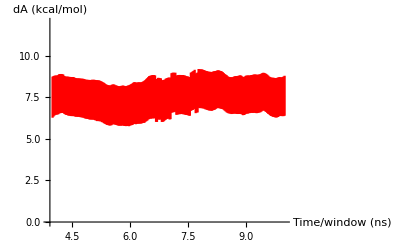

```mathematica
dAplotAll=ErrorListPlot[Partition[Riffle[Partition[Riffle[(Step-Step[[1]])/10000+SetStart,dA],2],Map[ErrorBar,Std]],2],
Joined->True,
PlotRange->{{SetStart-0.1,TotalRunNs},{0,magdA}},
AxesLabel->{"Time/window (ns)","dA (kcal/mol)"},
LabelStyle->Directive[FontSize->15],
PlotStyle->{Red}]
```

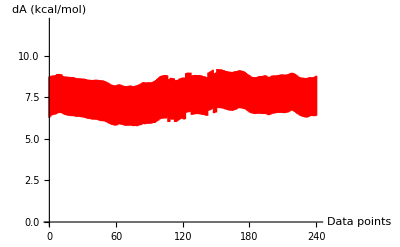

```mathematica
dAplotAllPoint=ErrorListPlot[Partition[Riffle[Partition[Riffle[(Step-Step[[1]])/((Step[[-1]]-Step[[1]])/(Length[Step]-1)),dA],2],Map[ErrorBar,Std]],2],
Joined->True,
PlotRange->{{0,Length[dA]},{0,magdA}},
AxesLabel->{"Data points","dA (kcal/mol)"},
LabelStyle->Directive[FontSize->15],
PlotStyle->{Red}]
```

```mathematica
startstep=Input["Start step",71]
```

1

```mathematica
VNTest[data_]:=
Module[{sum,n,j,qsquared,r,sigmar,ur},
sum=0;
n=Length[data];
For[j=1,j≤(n-1),j++,
sum=sum+(data[[j+1]]-data[[j]])^2];
qsquared=sum/(2*(n-1));
r=qsquared/Variance[data];
sigmar=((1+1/(n-1))/(n+1))^0.5;
ur=(r-1)/sigmar;
CDF[NormalDistribution[],ur]
]
```

```mathematica
parrayVN=Reap[For[i=1,i≤Round[Length[dA[[startstep;;-1]]]/5],i++,
Sow[VNTest[dA[[startstep;;-1;;i]]]];
];][[2,1]];
```

```mathematica
passVN=Reap[For[i=1,i≤Length[parrayVN],i++,
If[parrayVN[[i]]≥0.05,
Sow[{i,parrayVN[[i]]}];
];
];][[2,1]];
```

```mathematica
passVN
```

{{26,0.0718059},{28,0.0524761},{31,0.10089},{32,0.0842437},{33,0.161421},{34,0.146128},{35,0.159327},{36,0.109284},{37,0.150791},{38,0.276191},{39,0.237304},{40,0.184172},{41,0.251632},{42,0.192279},{43,0.14442},{44,0.105954},{45,0.271832},{46,0.371377},{47,0.21106},{48,0.388812}}

```mathematica
corrstep=passVN[[1,1]]
```

26

```mathematica
corrtest=AutocorrelationTest[dA[[startstep;;-1;;corrstep]],Automatic,"HypothesisTestData"];
```

```mathematica
pvalueVN=passVN[[1,2]]
```

0.0718059

```mathematica
model=LinearModelFit[dA[[startstep;;-1;;corrstep]],{1,x},x]
```

FittedModel[7.28645+0.0430725 x]

```mathematica
DvalueDW=model["DurbinWatsonD"]
```

1.4138

```mathematica
corrtest["PValueTable",All]
```

| P-Value
Box-Pierce | 0.301107
Ljung-Box | 0.143234

```mathematica
corrtest["PValue",All]
```

{0.301107,0.143234}

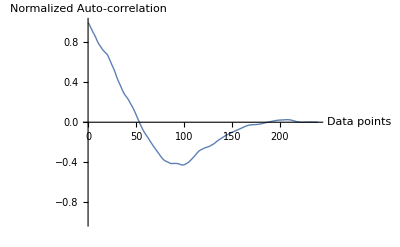

```mathematica
corr=ListLinePlot[Table[{i,CorrelationFunction[dA[[startstep;;-1]],i]},{i,0,Length[dA[[startstep;;-1]]]-1}],
PlotRange->{-1,1},
PlotStyle->Thick,
AxesLabel->{"Data points","Normalized Auto-correlation"},
LabelStyle->Directive[FontSize->15]]
```

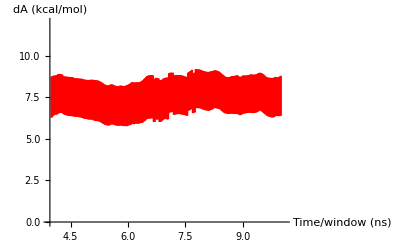

```mathematica
dAplot=ErrorListPlot[Partition[Riffle[Partition[Riffle[(Step-Step[[1]])/10000+SetStart,dA],2],Map[ErrorBar,Std]],2][[startstep;;-1]],
Joined->True,
PlotRange->{{SetStart+startstep*dStep/10000-0.1,TotalRunNs+0.1},{0,magdA}},
AxesLabel->{"Time/window (ns)","dA (kcal/mol)"},
LabelStyle->Directive[FontSize->15],
PlotStyle->{Red}]
```

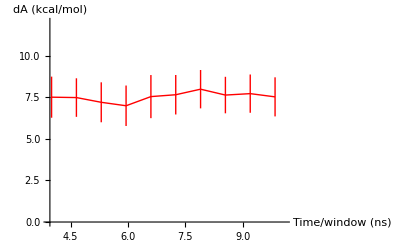

```mathematica
dAplottest=ErrorListPlot[Partition[Riffle[Partition[Riffle[(Step-Step[[1]])/10000+SetStart,dA],2],Map[ErrorBar,Std]],2][[startstep;;-1;;corrstep]],
Joined->True,
PlotRange->{{SetStart+startstep*dStep/10000-0.1,TotalRunNs+0.1},{0,magdA}},
AxesLabel->{"Time/window (ns)","dA (kcal/mol)"},
LabelStyle->Directive[FontSize->15],
PlotStyle->{Thick,Red}]
```

```mathematica
CreateDirectory["graphs"];
Export["graphs/dA_all.png",dAplotAll,ImageResolution->100];
Export["graphs/dA_all_points.png",dAplotAllPoint,ImageResolution->100];
Export["graphs/dA.png",dAplot,ImageResolution->100];
Export["graphs/dA_test.png",dAplottest,ImageResolution->100];
Export["graphs/corr_dA_points.png",corr,ImageResolution->100];
```

```mathematica
MKTest[data_]:=
Module[{big,n,j,k,S,sigmaS,uS},
big=0;
n=Length[data];
For[j=1,j≤(n-1),j++,
For[k=j+1,k≤n,k++,
If[data[[j]]>data[[k]],big=big+1];
];
];
S=2*big-Binomial[n,2];
sigmaS=(n*(n-1)*(2*n+5)/18)^0.5;
uS=S/sigmaS;
CDF[NormalDistribution[],uS]
]
```

```mathematica
testdata=dA[[startstep;;-1;;corrstep]];
```

```mathematica
pvalueMean=MKTest[testdata]
```

0.0641894

```mathematica
testStd=Std[[startstep;;-1;;corrstep]]/1.96;
```

```mathematica
pvalueStd=MKTest[testStd]
```

0.955379

```mathematica
Export["graphs/report.txt",
{"Skip: ",
StringJoin[ToString[SetSkip]," ns"],"",
"Start step: ",
startstep,"",
"Moving average time span:",
StringJoin[ToString[SetMA]," ns"],"",
"Correlation steps: ",
corrstep,"",
"Correlation time: ",
StringJoin[ToString[N[corrstep*dStep/10000]], " ns"],"",
"Number of data points: ",
Length[testdata],"",
"Auto-correlation test: ",
"p-value von Neumann: ",
pvalueVN,"",
"p-value LJung-Box: ",
corrtest["PValue",All][[2]],"",
"Durbin Watson D (good if between 1-3): ",
DvalueDW,"",
"MK trend test: ",
"p-value Mean: ",
pvalueMean,"",
"p-value Standard deviation: ",
pvalueStd
}
]
```

graphs/report.txt